## Population ODEs

This code implements the simplest version of the population dynamics: specify some strategies and run one simulation, then plot the results.

```mathematica
Clear["Global`*"]; 
precision=30;
$MinPrecision=precision;
SetDirectory[NotebookDirectory[]];
```

### Quasi-steady state functions

```mathematica
getPositions[pop0_]:=
Block[{m0,list,extendedPop},
m0=Length[pop0];
extendedPop=Join[{0},pop0];
Table[{Total[extendedPop[[1;;i-1]]],Total[extendedPop[[1;;i]]]},{i,2,m0+1}]
];

(*given a set of populations, determine the steady-state nutrient concentrations by requiring continuity and differentiability at population boundaries*)
getConcentration[n_,nutrient_]:=
Block[{i,m0,c,dc,m,cSys,cSysWrap,cSystem,dcSys,dcSysWrap,dcSystem,totalcSys,vars,aVars,bVars,z},
m0=Length[n];
aVars=ToExpression[Table["a"<>IntegerString[k],{k,m0}]];
bVars=ToExpression[Table["b"<>IntegerString[k],{k,m0}]];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
dc[a_,b_,α_,θ_]:=Sqrt[α/d]*(a*E^(Sqrt[α/d]*θ)-b*E^(-Sqrt[α/d]*θ));

(*  Create a system of eqs for c(θ) in each region *)
cSys=Table[c[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==c[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
cSysWrap=c[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==c[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
cSystem=Join[cSys,{cSysWrap}];

(*do the same thing for the derivatives of c(θ)*)
dcSys=Table[dc[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==dc[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
dcSysWrap=dc[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==dc[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
dcSystem=Join[dcSys,{dcSysWrap}];

totalcSys=Join[cSystem,dcSystem];
vars=Table[{aVars[[i]],bVars[[i]]},{i,m0}]//Flatten;
{z,m}=CoefficientArrays[totalcSys,vars];
LinearSolve[m,-z]  
];
(*returns {a1,b1,a2,b2...}: in a region σ c_i=a*E^(a*θ/d)+b*E^(-a*θ/d)+si/αi. *)

fullConcentration[n_,nutrient_]:=
Block[{a,b,c,coeff,positions,pieces,conditions,fullC},
coeff=getConcentration[n,nutrient];
positions=getPositions[n];
a=Table[coeff[[2*i-1]],{i,m}];
b=Table[coeff[[2*i]],{i,m}];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
pieces=Table[c[a[[j]],b[[j]],α[[j,nutrient]],theta-positions[[j,1]]],{j,m}];
conditions=Table[positions[[i,1]]<theta<=positions[[i,2]],{i,m}];
fullC=Piecewise[Transpose[{pieces,conditions}]]
];
```

### Dynamics

```mathematica
getGrowth[pop_,species_,c_]:=
Block[{growth,myN,myA,myB},
myN=pop[[species]];
myA=c[[species*2-1]];
myB=c[[species*2]];

growth=Table[α[[species,i]]*((s[[i]]*myN/α[[species,i]])+Sqrt[d/α[[species,i]]]*(myA[[i]]*(E^(myN*Sqrt[α[[species,i]]/d])-1)-myB[[i]]*(E^(-myN*Sqrt[α[[species,i]]/d])-1))),{i,p}]//Total
];
```

```mathematica
ndot[n_?(VectorQ[#, NumericQ]&)]:=
Block[{dn,growthTable,n0,nNew,cCoeff},
n0=n;
cCoeff=Transpose[Table[getConcentration[n0,v],{v,p}]];
growthTable=Table[getGrowth[n0,i,cCoeff],{i,Length[n0]}];
(*δ=Total[growthTable];*)
dn=growthTable-δ*n0
];
```

### Environmental parameters

```mathematica
supply=1;  (*total nutrient supply*)
δ=supply;   (*death rate*)
e=1;             (* total enzyme budget*)
```

```mathematica
d=1.;(*diffusion coefficient*)
l=20;     (*system size*)
s={.25,.45,.3}*supply;  (*nutrient supply vector, can be any length ≥2*)
p=Length[s];
```

### Species parameters: generate m random strategies

```mathematica
steps=1000;
```

```mathematica
(*uncomment if you want a reproducible set of strategies*)
(*SeedRandom[10]*)
```

```mathematica
m=10;        (*initial number of species*)
randomStrats[number_]:=RandomPoint[Simplex[e*IdentityMatrix[p]],number];
α=randomStrats[m];     (*random strategies*)
```

```mathematica
(*map strategies to a color scheme for visualization*)
colors=Table[XYZColor[α[[i]]],{i,m}]
```

{XYZColor[{0.4868967403239681, 0.0928425460454998, 0.4202607136305321}],XYZColor[{0.3725079758441834, 0.5680948436774087, 0.05939718047840792}],XYZColor[{0.12204733806430079, 0.5152046553976866, 0.36274800653801265}],XYZColor[{0.03070848087982503, 0.6660039963123228, 0.3032875228078522}],XYZColor[{0.07667635668561812, 0.6633290846308666, 0.2599945586835153}],XYZColor[{0.08572538598796031, 0.3845924049578784, 0.5296822090541613}],XYZColor[{0.5007361523986804, 0.17831086216413672, 0.32095298543718287}],XYZColor[{0.44139031701791054, 0.12525963302024912, 0.43335004996184034}],XYZColor[{0.5704547165029756, 0.19190729407399232, 0.23763798942303205}],XYZColor[{0.22278783181145068, 0.49239333370281124, 0.2848188344857381}]}

### Calculate n_σ(t) and plot

```mathematica
nInit=l*ConstantArray[1/m,m]//N;       (*initial conditions*)
```

```mathematica
AbsoluteTiming[sol=NDSolveValue[{n'[t]==ndot[n[t]],n[0]==nInit},n,{t,0,steps}]]
```

{1.53526,InterpolatingFunction[…]}

```mathematica
sol[steps]
```

{0.507471,0.579589,0.945887,2.03578×10^-6,0.377959,0.319051,0.595024,0.000330088,0.127445,16.5472}

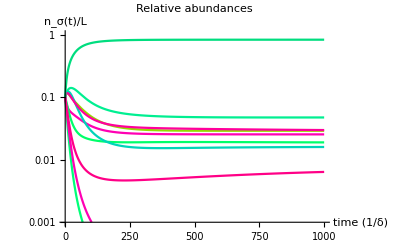

```mathematica
logSeriesPlot=LogPlot[Evaluate[Table[Indexed[sol[t],i]/l,{i,m}]],{t,0,steps},PlotRange->{Automatic,{10^-3,1}},TicksStyle->Black,PlotStyle->colors,LabelStyle->Directive[Black,12],AxesLabel->{"time (1/δ)","n_σ(t)/L"},PlotLabel->"Relative abundances"]
```

#### Visualize strategies on simplex (p=3)

```mathematica
stratSpace=Simplex[{{0,0,e},{0,e,0},{e,0,0}}];
```

```mathematica
mapToSimplex[point_]:=
Module[{},
newX=point[[2]]-point[[1]];
newY=Sqrt[3]*point[[3]];
{newX,newY}
];
```

```mathematica
remappedStrats=Table[{mapToSimplex[α[[i]]]},{i,m}];
supplyPoint=mapToSimplex[s];
```

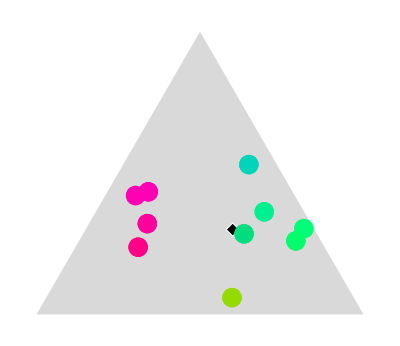

```mathematica
Show[Graphics[{LightGray,Triangle[{{-1,0},{1,0},{0,Sqrt[3]}}]}],ListPlot[remappedStrats,PlotStyle->colors,PlotMarkers->ConstantArray[{"•",20},m],PlotRange->{{-1,1},{0,Sqrt[3]}}],Graphics[{EdgeForm[{White}],Polygon[{supplyPoint+{-.04,0},supplyPoint+{0,.04},supplyPoint+{.04,0},supplyPoint+{0,-.04}}]}]]
```

### Concentration at steady state

```mathematica
c1Final=fullConcentration[sol[steps],1];
c2Final=fullConcentration[sol[steps],2];
c3Final=fullConcentration[sol[steps],3];
finalPositions=getPositions[sol[steps]];
```

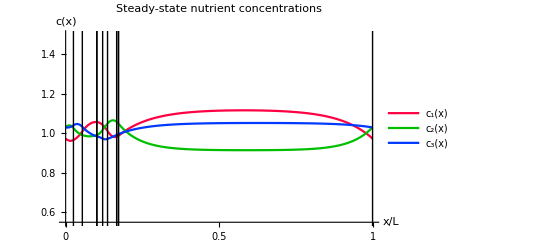

```mathematica
dividers=Table[Line[{{finalPositions[[i,2]],0},{finalPositions[[i,2]],10}}],{i,m}];
cPlot=Plot[{c1Final,c2Final,c3Final},{theta,0,l},PlotRange->{Full,{.55,1.5}},PlotStyle->{XYZColor[1,0,0],Darker[XYZColor[0,1,0],.25],XYZColor[0,0,1]},Ticks->{{{0,0},{l/2,.5},{l,1}},Automatic},TicksStyle->Black,
Epilog->{dividers},LabelStyle->Directive[12,Black],PlotLabel->"Steady-state nutrient concentrations",AxesLabel->{"x/L","c(x)"},PlotLegends->{"c_1(x)","c_2(x)","c_3(x)"}]
```

### Visualizing territories

```mathematica
sampleTimes=Range[0,75,1];  (*the period to visualize*)
numSamples=Length[sampleTimes];
```

```mathematica
popSamples=sol/@sampleTimes;
```

```mathematica
positionSamples=getPositions/@popSamples;
```

```mathematica
boundarySamples=Table[positionSamples[[i,j]]=positionSamples[[i,j]]//Last,{i,numSamples},{j,m}];
```

```mathematica
pairListTimeOrder=Table[Transpose[{boundarySamples[[i]],ConstantArray[sampleTimes[[i]],m]}],{i,numSamples}];
```

```mathematica
pairListSpeciesOrder=Transpose[pairListTimeOrder];
```

```mathematica
flippedPairListSpeciesOrder=Table[Reverse[pairListSpeciesOrder[[i,j]]],{i,m},{j,numSamples}];
```

```mathematica
fillingChart=Table[i->{{i-1},colors[[i]]},{i,2,m}];
fillingChart=Join[{1->{Axis,colors[[1]]}},fillingChart];
```

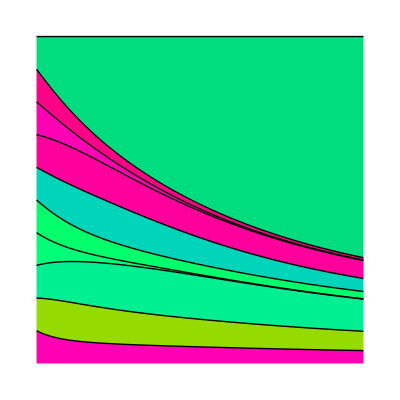

```mathematica
expA=ListLinePlot[flippedPairListSpeciesOrder,PlotStyle->Directive[Black,Thin],Filling->{fillingChart},Ticks->None,Axes->False,AspectRatio->1];
Rotate[expA,-Pi/2]
```